```mathematica
Nx=15;
Ny=15;
nx=15;
ny=15;
datrotuwsoca=Flatten[Import["trot_0.4_nutcalca.dat"]];
datrotdwsoca=Flatten[Import["trot_0.4_ndtcalca.dat"]];
datrotuwsocb=Flatten[Import["trot_0.4_nutcalcb.dat"]];
datrotdwsocb=Flatten[Import["trot_0.4_ndtcalcb.dat"]];
```

```mathematica
impdiffdata=Table[Partition[(datrotuwsoca+datrotdwsoca),3][[i,1]] + Partition[(datrotuwsoca+datrotdwsoca),3][[i,2]]+ Partition[(datrotuwsoca+datrotdwsoca),3][[i,3]],{i,1,Nx*Ny}]-4.03556;

diffdata=impdiffdata;
```

```mathematica
impdiffdatb=Table[Partition[(datrotuwsocb+datrotdwsocb),3][[i,1]] + Partition[(datrotuwsocb+datrotdwsocb),3][[i,2]]+ Partition[(datrotuwsocb+datrotdwsocb),3][[i,3]],{i,1,Nx*Ny}]-4.03556;

diffdatb=impdiffdatb;
```

```mathematica
plotdiffdata=Partition[Riffle[diffdata,Table[0,{i,Length[diffdata]}]],2*Sqrt[Length[diffdata]]];
plotdiffdatb=Partition[Riffle[Table[0,{i,Length[diffdatb]}],diffdatb],2*Sqrt[Length[diffdatb]]];
plotdiffdatab=Riffle[plotdiffdata,plotdiffdatb];
```

```mathematica
length=Sqrt[Length[diffdata]];
hlength=IntegerPart[length/2];
```

```mathematica
l=0;
For[i=1,i<=nx,i++,
For[j=1,j<=ny,j++,
xpos=(j-1) - (i - 1);
ypos=(j-1) + (i - 1);
l = l+1;
coorda[l] = {xpos,ypos};
];];
l=0;
For[i=1,i<=nx,i++,
For[j=1,j<=ny,j++,
xpos=(j-1) - (i - 1);
ypos=(j-1) + (i - 1)+1;
l = l+1;
coordb[l] = {xpos,ypos};
];];
rownumber=7;
countatom=7;

midatom=(nx*rownumber + countatom)+1;
midcoord=coorda[midatom];
```

```mathematica
For[l=1,l<=nx*ny,l++,
newcoorda[l] = coorda[l] - midcoord];
For[l=1,l<=nx*ny,l++,
newcoordb[l] = coordb[l] - midcoord];

ndiffdata = Table[Flatten[{newcoorda[l] ,diffdata[[l]]}],{l,1,nx*ny}];
ndiffdatb = Table[Flatten[{newcoordb[l] ,diffdatb[[l]]}],{l,1,nx*ny}];
```

```mathematica
alldiffdata= Join[ndiffdata ,ndiffdatb ];
limval = alldiffdata[[All,3]];
minval=Min[limval];
maxval=Max[limval];
```

```mathematica
squarelength=2;
xmax=squarelength;
xmin=-squarelength;
ymax=squarelength;
ymin=-squarelength;

posmidcoord = {0,0};
coordx1 = xmin;
coordy1 = ymin;
coordx2 = xmax;
coordy2 = ymin;
coordx3 = xmax;
coordy3 = ymax;
coordx4 = xmin;
coordy4 = ymax;

squareline=
{Blue,Thickness[0.01],Line[{{{coordx1,coordy1},{coordx2,coordy2}},{{coordx2,coordy2},{coordx3,coordy3}},{{coordx3,coordy3},{coordx4,coordy4}},{{coordx4,coordy4},{coordx1,coordy1}}}]};
```

```mathematica
pointlegend=BarLegend[{"Rainbow",{minval,maxval}},LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,24]}];
```

```mathematica
rmvpoints1=DeleteCases[Table[If[alldiffdata[[i,1]]>coordx3,pt=Null,If[alldiffdata[[i,2]]>coordy3,pt=Null,pt={alldiffdata[[i,1]],alldiffdata[[i,2]],alldiffdata[[i,3]]}]];pt,{i,1,Length[alldiffdata]}],Null];

rmvpoints2=DeleteCases[Table[If[rmvpoints1[[i,1]]<coordx1,pt=Null,If[rmvpoints1[[i,2]]<coordy1,pt=Null,pt={rmvpoints1[[i,1]],rmvpoints1[[i,2]],rmvpoints1[[i,3]]}]];pt,{i,1,Length[rmvpoints1]}],Null];
```

```mathematica
slimval=rmvpoints2[[All,3]];
sminval=Min[slimval];
smaxval=Max[slimval];
spointlegend=BarLegend[{"Rainbow",{sminval,smaxval}},LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,24]}];
```

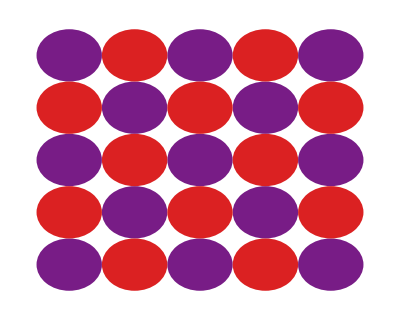

```mathematica
sqgraphicsplot = Graphics[Join[Table[{Blend["Rainbow",(rmvpoints2[[i,3]]-sminval)/(smaxval-sminval)],Rotate[Disk[{rmvpoints2[[i,1]],rmvpoints2[[i,2]]},{0.5,0.5}],0]},{i,1,Length[rmvpoints2]}]],ImagePadding->{{5,5},{5,5}},ImageSize->400,AspectRatio->0.8];

finsqgraphicsplot =sqgraphicsplot 
Export["finsqgraphicsplot.eps",finsqgraphicsplot];
```